```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynHelpers"};
$LoadTARCER=True;
$LoadFeynArts=True;
<<FeynCalc`
$FAVerbose=0
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.9 patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

TARCER 2.0, for description see the preprint hep-ph/9801383 at arxiv.org.

FeynHelpers 1.0.0 loaded.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", TUM-EFT 75/15, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

0

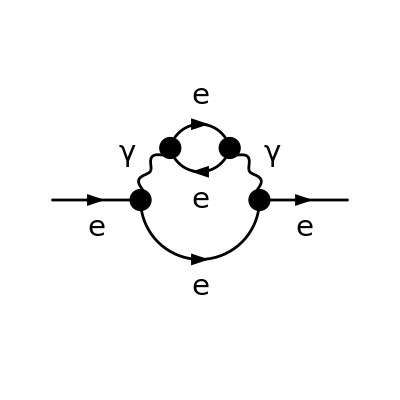

```mathematica
(* ::Subsection::*)
(*Electron self-energy*)


topsSE=CreateTopologies[2,1->1,ExcludeTopologies->{Tadpoles}];
diagsSE=InsertFields[topsSE,{F[2,{1}]}->{F[2,{1}]},InsertionLevel->{Particles},ExcludeParticles->{V[2|3],S[_],U[_],F[1|3|4]}];
Paint[DiagramExtract[diagsSE,{2}],ColumnsXRows->{3,1},SheetHeader->False,Numbering->None,ImageSize->{768,256}];
```

```mathematica
(* ::Text::*)
(*First of all we need to generate the amplitudes and convert them into FeynCalc notation.We choose l1 and l2 to be the loop momenta and p the external momentum*)


ampsSE=FCFAConvert[CreateFeynAmp[DiagramExtract[diagsSE,{2}],Truncated->True,PreFactor->-1],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{l1,l2},DropSumOver->True,ChangeDimension->D,UndoChiralSplittings->True,List->False,SMP->True,LorentzIndexNames->{μ}]//ReplaceAll[#,SMP["m_e"]->me]&//Contract//FCTraceFactor


(* ::Text::*)
(*Calculation of the Dirac trace,tensor reduction and simplification of the Dirac algebra*)


AbsoluteTiming[ampsSE1=(ampsSE/.DiracTrace->Tr)//FCMultiLoopTID[#,{l1,l2}]&//DiracSimplify];


(* ::Text::*)
(*Simplification of the loop integrals using shifts in the loop momenta*)


ampsSE2=ampsSE1//FDS[#,l1,l2]&;
```

(4 ⅈ e^4 (l1·l2) γ^Lor4.(γ·l1+me).γ^Lor4)/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))-(4 ⅈ e^4 (l2·p) γ^Lor4.(γ·l1+me).γ^Lor4)/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))+(4 ⅈ e^4 me^2 γ^Lor4.(γ·l1+me).γ^Lor4)/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))-(4 ⅈ e^4 l2^2 γ^Lor4.(γ·l1+me).γ^Lor4)/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))-(4 ⅈ e^4 (γ·l1).(γ·l1+me).(γ·l2))/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))-(4 ⅈ e^4 (γ·l2).(γ·l1+me).(γ·l1))/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))+(8 ⅈ e^4 (γ·l2).(γ·l1+me).(γ·l2))/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))+(4 ⅈ e^4 (γ·l2).(γ·l1+me).(γ·p))/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))+(4 ⅈ e^4 (γ·p).(γ·l1+me).(γ·l2))/((l1^2-me^2).(l2^2-me^2).(l1-p)^2.(l1-p)^2.((l1-l2-p)^2-me^2))

```mathematica
(* ::Text::*)
(*IBP-Reduction using FIRE*)


ampsSE3=FIREBurn[ampsSE2,{l1,l2},{p}]//FDS[#,l1,l2]&;
```

FIREBurn: Processing integral 1 of 13; IBP-reduction done, timing: 1.332
FIREBurn: Processing integral 2 of 13; IBP-reduction done, timing: 1.839
FIREBurn: Processing integral 3 of 13; IBP-reduction done, timing: 1.347
FIREBurn: Processing integral 4 of 13; IBP-reduction done, timing: 1.572
FIREBurn: Processing integral 5 of 13; IBP-reduction done, timing: 2.409
FIREBurn: Processing integral 6 of 13; IBP-reduction done, timing: 2.099
FIREBurn: Processing integral 7 of 13; IBP-reduction done, timing: 1.437
FIREBurn: Processing integral 8 of 13; IBP-reduction done, timing: 1.739
FIREBurn: Processing integral 9 of 13; IBP-reduction done, timing: 4.175
FIREBurn: Processing integral 10 of 13; IBP-reduction done, timing: 4.797
FIREBurn: Processing integral 11 of 13; IBP-reduction done, timing: 5.100
FIREBurn: Processing integral 12 of 13; IBP-reduction done, timing: 5.295
FIREBurn: Processing integral 13 of 13; IBP-reduction done, timing: 5.887

```mathematica
(* ::Text::*)
(*Nicer form*)


ampsSE4=ampsSE3//Collect2[#,{FeynAmpDenominator},Factoring->FullSimplify]&;


(* ::Text::*)
(*This is Sigma_2V(p^2) up to the 1/(2Pi)^2D prefactor*)


resSE=Cancel[ampsSE4/(-I FCI[(GSD[p])])]//FullSimplify;


(* ::Subsection::*)
(*Check with the literature*)


(* ::Text::*)
(*Check with Eq.5.51 from Grozin's Lectures on QED and QCD (hep-ph/0508242)*)
```

```mathematica
tfiamp0=ampsSE3//ToTFI[#,l1,l2,p]&;
SEFIRE=Simplify[TarcerRecurse[tfiamp0]];
```

```mathematica
SetOptions[DiracSlash,Dimension->D,FeynCalcInternal->True];SetOptions[DiracTrace,DiracTraceEvaluate->True];
t12=CreateTopologies[2,1->1,ExcludeTopologies->Internal];alldiags=InsertFields[t12,{F[02,{1}]}->{F[02,{1}]},InsertionLevel->{Particles},GenericModel->"/Users/jamesmckay/Documents/Programs/Mass_builder/models/QED2/QED2",Restrictions->{},Model->"/Users/jamesmckay/Documents/Programs/Mass_builder/models/QED2/QED2"];subdiags0=DiagramExtract[alldiags,1];
SPD[p,p]=mf^2;
amp0=FCFAConvert[CreateFeynAmp[subdiags0,Truncated->True],IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k1,k2},UndoChiralSplittings->True,TransversePolarizationVectors->{p},DropSumOver->True,List->False,ChangeDimension->D]//Contract//FCTraceFactor;amp0=amp0*256*Pi^8;masses=List[ma,mf,null];massesExpand=List[1,1,0];
amp0=amp0/.Index[Generation,1]->1;amp0=amp0/.Index[Generation,2]->2;amp0=amp0/.Index[Generation,3]->3;amp1=amp0//FDS[#,l1,l2]&;SetOptions[Eps,Dimension->D];fullamp0=(amp1)//DiracSimplify//FCMultiLoopTID[#,{k1,k2}]&//DiracSimplify;tfiamp0=fullamp0//ToTFI[#,k1,k2,p]&//ChangeDimension[#,D]&;
SE=Simplify[TarcerRecurse[tfiamp0]];
```

```mathematica
SE
```

1/(2 mf^2)EL^4 (-4 (D-2) γ·p A_{1,ma}^(D) B_({1,mf}{1,ma})^(D)+4 (D-2) γ·p A_{1,mf}^(D) B_({1,mf}{1,ma})^(D)+((D^2-2 D+4) mf^3+(D-2) (4 ma^2-D mf^2) γ·p) (B_({1,mf}{1,ma})^(D))^2+(((D^2-14 D+24) ma^4+4 (3 D-8) ma^2 mf^2+8 mf^4) γ·p-4 D ma^2 mf^3+8 mf^5) F_({1,ma}{1,mf}{1,mf}{1,ma}{1,mf})^(D)+2 (((D^2-11 D+18) ma^2+2 (D-4) mf^2) γ·p-2 D mf^3) V_({1,mf}{1,mf}{1,mf}{1,ma})^(D)-(D-4) (D-2) γ·p J_({1,mf}{1,ma}{1,ma})^(D)+(D-6) (D-2) γ·p J_({1,mf}{1,mf}{1,mf})^(D)+2 (D-2) γ·p K_({1,mf}{1,mf}{1,ma})^(D)+2 ((4 (D-2) ma^2-(D-4) D mf^2) γ·p+(D-2)^2 mf^3) V_({1,mf}{1,ma}{1,ma}{1,mf})^(D))

```mathematica
(SE-SEFIRE)/.mf->me
```

1/(30 me^4 p^2)(-1/((me^2-p^2)^3)2 (γ·p (9 (7 D^2-41 D+60) me^8+2 (72 D^2-585 D+1042) p^2 me^6+2 (51 D^2-241 D+286) p^4 me^4-2 (12 D^2-59 D+74) p^6 me^2+(3 D^2-17 D+24) p^8)-10 me^3 p^2 (3 (6 D^2-49 D+88) me^4+2 (18 D^2-99 D+136) p^2 me^2+(-6 D^2+25 D-24) p^4)) J_({1,me}{1,me}{1,me})^(D) me^2+(2 (9 me^2-p^2) (γ·p (3 (7 D-20) me^8+12 (4 D-21) p^2 me^6+2 (17 D-44) p^4 me^4+4 (5-2 D) p^6 me^2+(D-4) p^8)-20 me^3 p^2 (3 (D-5) me^4+6 (D-3) p^2 me^2-(D-1) p^4)) J_({2,me}{1,me}{1,me})^(D) me^2)/((me^2-p^2)^3)+1/((D-5) (D-3) (me^2-p^2)^3)(D-2) (10 (D-2) p^2 ((2 D^2+D-51) me^4-2 (10 D^2-77 D+139) p^2 me^2+(2 D^2-11 D+9) p^4) me^3+γ·p ((D^3-12 D^2+47 D-60) me^8+2 (18 D^3-247 D^2+1011 D-1166) p^2 me^6+2 (35 D^3-322 D^2+919 D-848) p^4 me^4-2 (6 D^3-53 D^2+153 D-154) p^6 me^2+(D^3-12 D^2+47 D-60) p^8)) (A_{1,me}^(D))^2-(D-2) (20 (D-1) p^2 me^3+(D-4) γ·p (me^2-p^2)^2) A_{1,me}^(D) B_({1,me}{1,0})^(D)) EL^4+1/(30 me^4 p^2)ⅈ e^4 (-(2 (γ·p (9 (7 D^2-41 D+60) me^8+2 (72 D^2-585 D+1042) p^2 me^6+2 (51 D^2-241 D+286) (p^2)^2 me^4-2 (12 D^2-59 D+74) (p^2)^3 me^2+(3 D^2-17 D+24) (p^2)^4)-10 (3 D-8) me^3 p^2 (3 (2 D-11) me^4+2 (6 D-17) p^2 me^2+(3-2 D) (p^2)^2)) J_({1,me}{1,me}{1,me})^(D) me^2)/((me^2-p^2)^3)+(2 (9 me^2-p^2) (γ·p (3 (7 D-20) me^8+12 (4 D-21) p^2 me^6+2 (17 D-44) (p^2)^2 me^4+4 (5-2 D) (p^2)^3 me^2+(D-4) (p^2)^4)-20 me^3 p^2 (3 (D-5) me^4+6 (D-3) p^2 me^2-(D-1) (p^2)^2)) J_({2,me}{1,me}{1,me})^(D) me^2)/((me^2-p^2)^3)+1/((D-5) (D-3) (me^2-p^2)^3)(D-2) (10 (D-2) p^2 ((2 D^2+D-51) me^4-2 (10 D^2-77 D+139) p^2 me^2+(2 D^2-11 D+9) (p^2)^2) me^3+γ·p ((D^3-12 D^2+47 D-60) me^8+2 (18 D^3-247 D^2+1011 D-1166) p^2 me^6+2 (35 D^3-322 D^2+919 D-848) (p^2)^2 me^4-2 (6 D^3-53 D^2+153 D-154) (p^2)^3 me^2+(D^3-12 D^2+47 D-60) (p^2)^4)) (A_{1,me}^(D))^2-(D-2) (20 (D-1) p^2 me^3+(D-4) γ·p (me^2-p^2)^2) A_{1,me}^(D) B_({1,me}{1,0})^(D))

```mathematica
testA=Coefficient[SE,TJI[D,Pair[Momentum[p,D],Momentum[p,D]],{{2,mf},{1,mf},{1,mf}}]]
```

(EL^4 (9 mf^2-p^2) ((3 (7 D-20) mf^8+12 (4 D-21) mf^6 p^2+2 (17 D-44) mf^4 p^4+4 (5-2 D) mf^2 p^6+(D-4) p^8) γ·p-20 mf^3 p^2 (3 (D-5) mf^4+6 (D-3) mf^2 p^2-(D-1) p^4)))/(15 mf^2 p^2 (mf^2-p^2)^3)

```mathematica
testB=Coefficient[SEFIRE,TJI[D,SPD[p,p],{{2,me},{1,me},{1,me}}]]
```

-(ⅈ e^4 (9 me^2-p^2) ((3 (7 D-20) me^8+12 (4 D-21) me^6 p^2+2 (17 D-44) me^4 (p^2)^2+4 (5-2 D) me^2 (p^2)^3+(D-4) (p^2)^4) γ·p-20 me^3 p^2 (3 (D-5) me^4+6 (D-3) me^2 p^2-(D-1) (p^2)^2)))/(15 me^2 p^2 (me^2-p^2)^3)

```mathematica
SE
```

1/(30 mf^4 p^2)EL^4 (-(D-2) (20 (D-1) mf^3 p^2+(D-4) (mf^2-p^2)^2 γ·p) A_{1,mf}^(D) B_({1,mf}{1,0})^(D)+1/((D-5) (D-3) (mf^2-p^2)^3)(D-2) (10 (D-2) mf^3 p^2 ((2 D^2+D-51) mf^4-2 (10 D^2-77 D+139) mf^2 p^2+(2 D^2-11 D+9) p^4)+((D^3-12 D^2+47 D-60) mf^8+2 (18 D^3-247 D^2+1011 D-1166) mf^6 p^2+2 (35 D^3-322 D^2+919 D-848) mf^4 p^4-2 (6 D^3-53 D^2+153 D-154) mf^2 p^6+(D^3-12 D^2+47 D-60) p^8) γ·p) (A_{1,mf}^(D))^2-(2 mf^2 ((9 (7 D^2-41 D+60) mf^8+2 (72 D^2-585 D+1042) mf^6 p^2+2 (51 D^2-241 D+286) mf^4 p^4-2 (12 D^2-59 D+74) mf^2 p^6+(3 D^2-17 D+24) p^8) γ·p-10 mf^3 p^2 (3 (6 D^2-49 D+88) mf^4+2 (18 D^2-99 D+136) mf^2 p^2+(-6 D^2+25 D-24) p^4)) J_({1,mf}{1,mf}{1,mf})^(D))/((mf^2-p^2)^3)+(2 mf^2 (9 mf^2-p^2) ((3 (7 D-20) mf^8+12 (4 D-21) mf^6 p^2+2 (17 D-44) mf^4 p^4+4 (5-2 D) mf^2 p^6+(D-4) p^8) γ·p-20 mf^3 p^2 (3 (D-5) mf^4+6 (D-3) mf^2 p^2-(D-1) p^4)) J_({2,mf}{1,mf}{1,mf})^(D))/((mf^2-p^2)^3))

```mathematica
SEFIRE
```

-1/(30 me^4 p^2)ⅈ e^4 (-(D-2) (20 (D-1) me^3 p^2+(D-4) (me^2-p^2)^2 γ·p) A_{1,me}^(D) B_({1,me}{1,0})^(D)+1/((D-5) (D-3) (me^2-p^2)^3)(D-2) (10 (D-2) me^3 p^2 ((2 D^2+D-51) me^4-2 (10 D^2-77 D+139) me^2 p^2+(2 D^2-11 D+9) (p^2)^2)+((D^3-12 D^2+47 D-60) me^8+2 (18 D^3-247 D^2+1011 D-1166) me^6 p^2+2 (35 D^3-322 D^2+919 D-848) me^4 (p^2)^2-2 (6 D^3-53 D^2+153 D-154) me^2 (p^2)^3+(D^3-12 D^2+47 D-60) (p^2)^4) γ·p) (A_{1,me}^(D))^2-(2 me^2 ((9 (7 D^2-41 D+60) me^8+2 (72 D^2-585 D+1042) me^6 p^2+2 (51 D^2-241 D+286) me^4 (p^2)^2-2 (12 D^2-59 D+74) me^2 (p^2)^3+(3 D^2-17 D+24) (p^2)^4) γ·p-10 (3 D-8) me^3 p^2 (3 (2 D-11) me^4+2 (6 D-17) me^2 p^2+(3-2 D) (p^2)^2)) J_({1,me}{1,me}{1,me})^(D))/((me^2-p^2)^3)+(2 me^2 (9 me^2-p^2) ((3 (7 D-20) me^8+12 (4 D-21) me^6 p^2+2 (17 D-44) me^4 (p^2)^2+4 (5-2 D) me^2 (p^2)^3+(D-4) (p^2)^4) γ·p-20 me^3 p^2 (3 (D-5) me^4+6 (D-3) me^2 p^2-(D-1) (p^2)^2)) J_({2,me}{1,me}{1,me})^(D))/((me^2-p^2)^3))

```mathematica
ampsSE3
```

(ⅈ (-2 D^2 γ·p me^4-5 D γ·p me^4+18 γ·p me^4+4 D^2 p^2 me^3-20 D p^2 me^3+24 p^2 me^3-4 D^2 γ·p p^2 me^2+38 D γ·p p^2 me^2-48 γ·p p^2 me^2+4 D^2 p^4 me-20 D p^4 me+24 p^4 me-2 D^2 γ·p p^4+31 D γ·p p^4-90 γ·p p^4) e^4)/(3 l1^2.(l2^2-me^2).((l1-p)^2-me^2) p^2 (p^2-me^2)^2)-(ⅈ γ·p (3 D^2 me^6-24 D me^6+36 me^6-5 D^2 p^2 me^4+30 D p^2 me^4-10 p^2 me^4+9 D^2 p^4 me^2-8 D p^4 me^2-100 p^4 me^2-7 D^2 p^6+42 D p^6-46 p^6) e^4)/(5 me^2 l1^2.((l1-l2)^2-me^2).((l1-p)^2-me^2) (me^2-p^2)^2 p^2)-(ⅈ (D-2) (-8 D γ·p me^6+37 γ·p me^6+16 D p^2 me^5-74 p^2 me^5-16 D γ·p p^2 me^4+51 γ·p p^2 me^4+16 D p^4 me^3-52 p^4 me^3-8 D γ·p p^4 me^2+51 γ·p p^4 me^2-2 p^6 me-11 γ·p p^6) e^4)/(3 (l1^2-me^2).((l2-l1)^2-me^2) p^2 (p^2-me^2)^4)+(ⅈ (D-2) l1^2 (30 D γ·p me^6-89 γ·p me^6-60 D p^2 me^5+298 p^2 me^5+90 D γ·p p^2 me^4-395 γ·p p^2 me^4-120 D p^4 me^3+372 p^4 me^3+50 D γ·p p^4 me^2-231 γ·p p^4 me^2+20 D p^6 me-30 p^6 me-10 D γ·p p^6+75 γ·p p^6) e^4)/(3 (l2^2-me^2).((l1-l2)^2-me^2).((l1-p)^2-me^2) p^2 (p^2-me^2)^4)-(ⅈ (D-2) (16 D γ·p me^6-63 γ·p me^6-32 D p^2 me^5+174 p^2 me^5+56 D γ·p p^2 me^4-193 γ·p p^2 me^4-80 D p^4 me^3+236 p^4 me^3+32 D γ·p p^4 me^2-201 γ·p p^4 me^2+16 D p^6 me-26 p^6 me-8 D γ·p p^6+73 γ·p p^6) e^4)/(3 (l1^2-me^2).((l2-p)^2-me^2) p^2 (p^2-me^2)^4)-(8 ⅈ (D-2) (l1·p) (6 D γ·p me^6-19 γ·p me^6-12 D p^2 me^5+62 p^2 me^5+18 D γ·p p^2 me^4-79 γ·p p^2 me^4-24 D p^4 me^3+72 p^4 me^3+10 D γ·p p^4 me^2-45 γ·p p^4 me^2+4 D p^6 me-6 p^6 me-2 D γ·p p^6+15 γ·p p^6) e^4)/(3 (l1^2-me^2).((l1-l2)^2-me^2).((l2-p)^2-me^2) p^2 (p^2-me^2)^4)-(2 ⅈ (9 me^2-p^2) (3 D γ·p me^6-9 γ·p me^6-6 D p^2 me^5+30 p^2 me^5+9 D γ·p p^2 me^4-39 γ·p p^2 me^4-12 D p^4 me^3+36 p^4 me^3+5 D γ·p p^4 me^2-23 γ·p p^4 me^2+2 D p^6 me-2 p^6 me-D γ·p p^6+7 γ·p p^6) e^4)/(3 (l1^2-me^2).((l1-l2)^2-me^2).((l1-l2)^2-me^2).((l2-p)^2-me^2) (me^2-p^2)^3 p^2)+1/(3 me^2 l1^2.((l1-l2)^2-me^2).((l1-p)^2-me^2) (me^2-p^2)^2 p^2)ⅈ (D^2 γ·p me^6+8 D γ·p me^6-20 γ·p me^6-2 D^2 p^2 me^5+14 D p^2 me^5-20 p^2 me^5+5 D^2 γ·p p^2 me^4-11 D γ·p p^2 me^4-34 γ·p p^2 me^4-8 D^2 p^4 me^3+32 D p^4 me^3-32 p^4 me^3+3 D^2 γ·p p^4 me^2-22 D γ·p p^4 me^2+44 γ·p p^4 me^2+2 D^2 p^6 me-6 D p^6 me+4 p^6 me-D^2 γ·p p^6+9 D γ·p p^6-14 γ·p p^6) e^4+(ⅈ γ·p (9 me^2-p^2) (9 D me^8-30 me^8+42 D p^2 me^6-138 p^2 me^6+16 D p^4 me^4-142 p^4 me^4-2 D p^6 me^2+50 p^6 me^2-D p^8+4 p^8) e^4)/(15 me^2 (l1^2-me^2).(l1^2-me^2).((l1-l2)^2-me^2).((l2-p)^2-me^2) (me^2-p^2)^3 p^2)+(ⅈ γ·p (29 D^2 me^8-180 D me^8+244 me^8-44 D^2 p^2 me^6-66 D p^2 me^6+728 p^2 me^6+50 D^2 p^4 me^4-174 D p^4 me^4-92 p^4 me^4-36 D^2 p^6 me^2+186 D p^6 me^2-168 p^6 me^2+D^2 p^8-6 D p^8+8 p^8) e^4)/(30 me^4 l1^2.(l2^2-me^2).((l1-p)^2-me^2) (me^2-p^2)^2 p^2)+(2 ⅈ γ·p (18 D^2 me^8-108 D me^8+144 me^8+56 D^2 p^2 me^6-285 D p^2 me^6+421 p^2 me^6+42 D^2 p^4 me^4-357 D p^4 me^4+381 p^4 me^4-28 D^2 p^6 me^2+225 D p^6 me^2-233 p^6 me^2+8 D^2 p^8-51 D p^8+55 p^8) e^4)/(15 me^2 (l1^2-me^2).((l2-l1)^2-me^2) (me^2-p^2)^4 p^2)-(2 ⅈ γ·p (14 D^2 me^8-81 D me^8+106 me^8+6 D^2 p^2 me^6-93 D p^2 me^6+237 p^2 me^6+28 D^2 p^4 me^4-63 D p^4 me^4-151 p^4 me^4-26 D^2 p^6 me^2+105 D p^6 me^2-p^6 me^2+10 D^2 p^8-60 D p^8+65 p^8) e^4)/(15 me^2 (l1^2-me^2).((l2-p)^2-me^2) (me^2-p^2)^4 p^2)-(4 ⅈ γ·p (l1·p) (32 D^2 me^8-189 D me^8+250 me^8+62 D^2 p^2 me^6-378 D p^2 me^6+658 p^2 me^6+70 D^2 p^4 me^4-420 D p^4 me^4+230 p^4 me^4-54 D^2 p^6 me^2+330 D p^6 me^2-234 p^6 me^2+18 D^2 p^8-111 D p^8+120 p^8) e^4)/(15 me^2 (l1^2-me^2).((l1-l2)^2-me^2).((l2-p)^2-me^2) (me^2-p^2)^4 p^2)+(ⅈ γ·p l1^2 (5 D^2 me^8-48 D me^8+76 me^8-64 D^2 p^2 me^6+282 D p^2 me^6-158 p^2 me^6+22 D^2 p^4 me^4+126 D p^4 me^4-670 p^4 me^4-48 D^2 p^6 me^2+150 D p^6 me^2+102 p^6 me^2+21 D^2 p^8-126 D p^8+138 p^8) e^4)/(15 me^2 (l2^2-me^2).((l1-l2)^2-me^2).((l1-p)^2-me^2) (me^2-p^2)^4 p^2)-1/(3 (l1^2-me^2).((l1-l2)^2-me^2).((l2-p)^2-me^2) p^2 (p^2-me^2)^4)2 ⅈ (6 D^2 γ·p me^8-19 D γ·p me^8+5 γ·p me^8-12 D^2 p^2 me^7+62 D p^2 me^7-34 p^2 me^7+24 D^2 γ·p p^2 me^6-136 D γ·p p^2 me^6+142 γ·p p^2 me^6-36 D^2 p^4 me^5+210 D p^4 me^5-298 p^4 me^5+28 D^2 γ·p p^4 me^4-194 D γ·p p^4 me^4+296 γ·p p^4 me^4-20 D^2 p^6 me^3+130 D p^6 me^3-198 p^6 me^3+8 D^2 γ·p p^6 me^2-56 D γ·p p^6 me^2+114 γ·p p^6 me^2+4 D^2 p^8 me-18 D p^8 me+18 p^8 me-2 D^2 γ·p p^8+21 D γ·p p^8-45 γ·p p^8) e^4-1/(6 (D-5) (D-3) me^2 (l1^2-me^2).((l2-l1)^2-me^2) (me^2-p^2)^4 p^2)ⅈ (D-2) (42 D^3 γ·p me^8-463 D^2 γ·p me^8+1637 D γ·p me^8-1872 γ·p me^8-84 D^3 p^2 me^7+1094 D^2 p^2 me^7-4594 D p^2 me^7+6144 p^2 me^7+120 D^3 γ·p p^2 me^6-1476 D^2 γ·p p^2 me^6+5918 D γ·p p^2 me^6-7666 γ·p p^2 me^6-156 D^3 p^4 me^5+1666 D^2 p^4 me^5-5754 D p^4 me^5+6548 p^4 me^5+52 D^3 γ·p p^4 me^4-662 D^2 γ·p p^4 me^4+2760 D γ·p p^4 me^4-3750 γ·p p^4 me^4+52 D^3 p^6 me^3-486 D^2 p^6 me^3+1386 D p^6 me^3-1208 p^6 me^3-24 D^3 γ·p p^6 me^2+324 D^2 γ·p p^6 me^2-1406 D γ·p p^6 me^2+1906 γ·p p^6 me^2-4 D^3 p^8 me+30 D^2 p^8 me-62 D p^8 me+36 p^8 me+2 D^3 γ·p p^8-27 D^2 γ·p p^8+115 D γ·p p^8-138 γ·p p^8) e^4-(ⅈ γ·p (32 D^2 me^10-234 D me^10+376 me^10-6 D^2 p^2 me^8-31 D p^2 me^8+310 p^2 me^8-160 D^2 p^4 me^6+896 D p^4 me^6-1528 p^4 me^6-188 D^2 p^6 me^4+1502 D p^6 me^4-2028 p^6 me^4+80 D^2 p^8 me^2-686 D p^8 me^2+912 p^8 me^2-14 D^2 p^10+89 D p^10-90 p^10) e^4)/(15 me^2 (l1^2-me^2).((l1-l2)^2-me^2).((l2-p)^2-me^2) (me^2-p^2)^4 p^2)-1/(30 (D-5) (D-3) me^4 (l1^2-me^2).((l2-l1)^2-me^2) (me^2-p^2)^4 p^2)ⅈ γ·p (37 D^4 me^10-536 D^3 me^10+2807 D^2 me^10-6256 D me^10+4980 me^10+7 D^4 p^2 me^8-222 D^3 p^2 me^8+2101 D^2 p^2 me^8-7722 D p^2 me^8+9604 p^2 me^8+134 D^4 p^4 me^6-1612 D^3 p^4 me^6+6166 D^2 p^4 me^6-6980 D p^4 me^6-1932 p^4 me^6-86 D^4 p^6 me^4+1056 D^3 p^6 me^4-4238 D^2 p^6 me^4+5664 D p^6 me^4-188 p^6 me^4+37 D^4 p^8 me^2-492 D^3 p^8 me^2+2323 D^2 p^8 me^2-4572 D p^8 me^2+3016 p^8 me^2-D^4 p^10+14 D^3 p^10-71 D^2 p^10+154 D p^10-120 p^10) e^4-(ⅈ (D-4) (D-2) (D-1) γ·p e^4)/(2 (D-5) (D-3) me^2 (l1^2-me^2).((l2-l1)^2-me^2) p^2)